High order Ne.b4de.b4lec elements with local complete sequence properties
	Joachim Scho.a8berl and Sabine Zaglmayr

```mathematica
Needs["VectorAnalysis`"]
SetCoordinates[Cartesian[x,y,z]];
```

the Legendrepolynomials       l_i(x)  (i=0,...p)
	l_i(x):=ix

```mathematica
l(i_,x_):=ix;
```

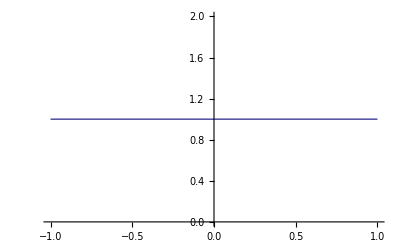
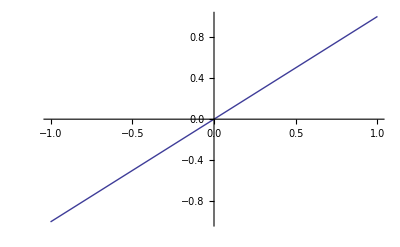
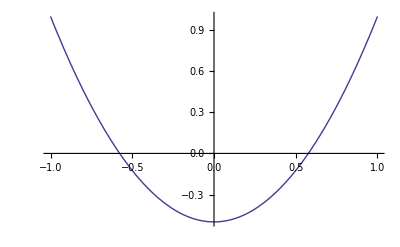
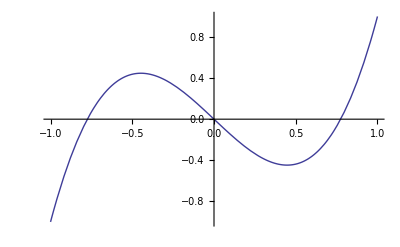
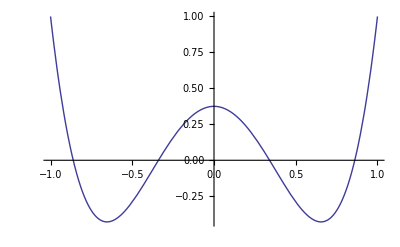
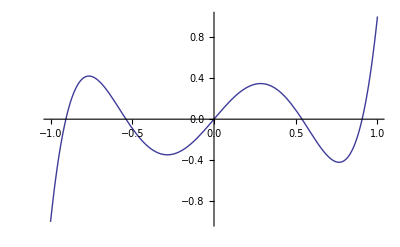

```mathematica
Table[Plot[l[i, x], {x,-1,1}], {i,0,5}]
```

theintegratedLegendre-polynomialsL_i(i=2,...,p)
L_i_[x_]:=∫_-1^x i-1zⅆz

```mathematica
L(i_,x_):=∫_-1^x l(i-1,z)ⅆz
```

```mathematica
For[i=2,i≤6,i++,    L(i,x_)=∫_-1^x l(i-1,z)ⅆz     ]
```

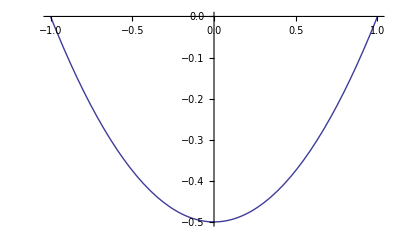
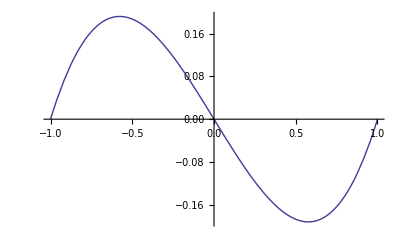
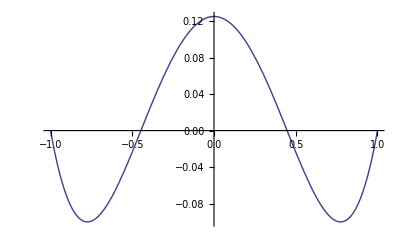
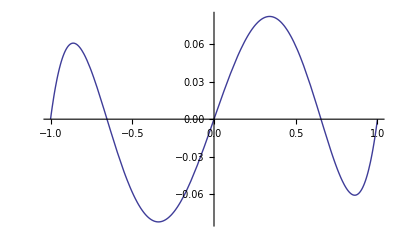

```mathematica
Table[Plot[L(i,x),{x,-1,1}],{i,2,5}]
```

the scaled Legendre polynomials

```mathematica
lS(n_,s_,t_):=Simplify[t^n l(n,s/t)];
```

```mathematica
Table[Plot3D[lS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the scaled integrated Legendre polynomials

```mathematica
LS(n_,s_,t_):=Simplify[t^n L(n,s/t)];
```

```mathematica
Table[Plot3D[LS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,2,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the barycentric coordinates
	λ_i (i=1,2,3)

```mathematica
x1=0;y1=0;
x2=1;y2=0;
x3=0;y3=1;
sol=Solve[{x1*lam1+x2*lam2+x3*lam3==x,
y1*lam1+y2*lam2+y3*lam3==y,
lam1+lam2+lam3==1},
{lam1,lam2,lam3}];
lamda[1,x_,y_]=lam1/.sol[[1]];
lamda[2,x_,y_]=lam2/.sol[[1]];
lamda[3,x_,y_]=lam3/.sol[[1]];
```

```mathematica
Table[Plot3D[lamda[i,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z}, 1>s+t]],
{i,1,3}]
Table[lamda[i,s,t],{i,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{1-s-t,s,t}

Hierarchical triangular H1- element  of order p using Scaled Legendre Polynomials

Vertex - based functions

```mathematica
phiV[i_,s_,t_]:=lamda[i,s,t];
```

Edge - based functions

```mathematica
Edge[1]={1,2}; Edge[2]={2,3}; Edge[3]={1,3};
Clear[phiE];
phiE[m_,i_,s_,t_]:=LS[i, 
lamda[Edge[m][[1]],s,t]- lamda[Edge[m][[2]],s,t],
	lamda[Edge[m][[2]],s,t]+ lamda[Edge[m][[1]],s,t] ]
```

Interior functions

```mathematica
u[i_,s_,t_]:=LS[i, lamda[2,s,t]- lamda[1,s,t],lamda[1,s,t]+ lamda[2,s,t] ];
v[j_,s_,t_]:= lamda[3,s,t]*(l[j-1,lamda[3,s,t]-lamda[1,s,t]-lamda[2,s,t]]);
phiI[i_,j_,s_,t_]:=u[i,s,t]*v[j,s,t];
```

p=1
Vertex - based functions

```mathematica
Table[Plot3D[phiV[i,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z}, 1>s+t]],
{i,1,3}]
{phiV[1,s,t], phiV[2,s,t], phiV[3,s,t]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{1-s-t,s,t}

p=2
Edge - based functions

```mathematica
p=2;
Table[Plot3D[phiE[m,p,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{m,1,3}]
Table[phiE[m,p,s,t],{m,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 s (-1+s+t),-2 s t,2 t (-1+s+t)}

p=3
Edge - based functions

```mathematica
p=3;
Table[Plot3D[phiE[m,p,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{m,1,3}]
Factor[Table[phiE[m,p,s,t],{m,1,3}]]/.-1+s+t->-r
{-2 s (s-t) t,-2 r t (t-r),-2 r s (r-s)}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 r s (-1+2 s+t),-2 s (s-t) t,2 r t (-1+s+2 t)}

{-2 s (s-t) t,-2 r t (-r+t),-2 r (r-s) s}

Interior functions

```mathematica
Table[Plot3D[phiI[p-k,k,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{k,1,p-2}]
Factor[Table[phiI[p-k,k,s,t],{k,1,p-2}]]
```

{-Graphics3D-}

{2 s t (-1+s+t)}

p=4
Edge - based functions

```mathematica
p=4;
Table[Plot3D[phiE[m,p,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{m,1,3}]
Factor[Table[phiE[m,p,s,t],{m,1,3}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 s (-1+s+t) (1-5 s+5 s^2-2 t+5 s t+t^2),-2 s t (s^2-3 s t+t^2),2 t (-1+s+t) (1-2 s+s^2-5 t+5 s t+5 t^2)}

Interior functions

```mathematica
Table[Plot3D[phiI[p-k,k,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{k,1,p-2}]
Factor[Table[phiI[p-k,k,s,t],{k,1,p-2}]]
```

{-Graphics3D-,-Graphics3D-}

{2 s t (-1+s+t) (-1+2 s+t),2 s t (-1+s+t) (-1+2 t)}

p=5
Edge - based functions

```mathematica
p=5;
Table[Plot3D[phiE[m,p,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{m,1,3}]
Factor[Table[phiE[m,p,s,t],{m,1,3}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 s (-1+s+t) (-1+2 s+t) (1-7 s+7 s^2-2 t+7 s t+t^2),-2 s (s-t) t (s^2-5 s t+t^2),-2 t (-1+s+t) (-1+s+2 t) (1-2 s+s^2-7 t+7 s t+7 t^2)}

Interior functions

```mathematica
Table[Plot3D[phiI[p-k,k,s,t],{s,0,1},{t,0,1},RegionFunction->Function[{s,t,z},1>s+t]],{k,1,p-2}]
Factor[Table[phiI[p-k,k,s,t],{k,1,p-2}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 s t (-1+s+t) (1-5 s+5 s^2-2 t+5 s t+t^2),2 s t (-1+s+t) (-1+2 s+t) (-1+2 t),2 s t (-1+s+t) (1-6 t+6 t^2)}

```mathematica
Arrows[vec0_]:=Module[{vec=vec0, ndiv,i, j, d,arrows, l1,l2,l3,xp,yp,zp, point,arrow , fac, v, len, maxlen},
ndiv=10;
fac=10;
d=1/ndiv;
maxlen=0.;
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
v=vec[xp,yp,zp];
len=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
If[maxlen<len, maxlen=len, maxlen];
];
];

arrows={};
For[j=0, j≤ndiv, j++,
l3=d*j;
For[i=0,i≤ndiv-j, i++,
l2=d*i;
li=1-l2-l3;
xp=l1*x1+l2*x2+l3*x3;
yp=l1*y1+l2*y2+l3*y3;
zp=0;
point={xp,yp,zp}*fac;
arrow={point, point+vec[xp,yp,zp]/maxlen*2};
arrows=Append[arrows,Arrow[arrow]];
];
];
arrows
]

G3[vec_]:=Module[{fac, tri},
fac=10;
tri=Polygon[{{0,0,0}*fac,{1,0,0}*fac,{0,1,0}*fac}];
Graphics3D[{{Arrowheads[.04],Thick,Arrows[vec]}, {EdgeForm[Thick],Opacity[0],tri}},ViewPoint->{0,0,Infinity}, ImageSize->Small,Boxed->False]
];
```

Hierarchical triangular Hcurl - element of order p using Scaled Legendre Polynomials

Edge - based shape functions

Edge - element shape function

```mathematica
Ne[m_,1,x_, y_,z_]:=-Grad[lamda[Edge[m][[1]], x,y]]*lamda[Edge[m][[2]],x,y]+lamda[Edge[m][[1]], x,y]*Grad[lamda[Edge[m][[2]],x,y]];
```

High order edge-based functions

```mathematica
Ne[m_,i_,x_, y_,z_]:=Simplify[Grad[phiE[m,i,x,y]]]
```

Element - based shape functions

Type 1 : gradient fields

```mathematica
NI1[i_,j_,x_, y_,z_]:=Grad[phiI[i,j,x,y]];
```

Type 2 :

```mathematica
NI2[i_,j_,x_, y_,z_]:=Grad[u[i,x,y]] *v[j, x, y] -u[i, x, y]*Grad[v[j,x,y]];
```

Type 3 :

```mathematica
NI3[j_,x_, y_,z_]:=(Grad[lamda[1,x,y]] *lamda[2, x, y] -lamda[1, x, y]*Grad[lamda[2,x,y]])* v[j,x,y];
```

p=1
Edge - element shape function

```mathematica
p=1;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p,x, y,z]];
Table[G3[vec[m]],{m,1,3}]
Table[vec[m][x,y,z],{m,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{1-y,x,0},{-y,x,0},{y,1-x,0}}

p=2
High order edge-based functions  gradient fields

```mathematica
p=2;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
Table[vec[m][x,y,z],{m,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 (-1+2 x+y),2 x,0},{-2 y,-2 x,0},{2 y,2 (-1+x+2 y),0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-}

{{2 y (-1+2 x+y),2 x (-1+x+2 y),0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-}

{{2 y (-1+2 x+y),-2 (-1+x) x,0}}

Type 3 :

```mathematica
For[k=1, k≤1, k++, vec[k][x_,y_,z_]=NI3[p-1,x, y,z]];
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[k]],{k,1,1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,1}]]
```

{-Graphics3D-}

{{(-1+y) y,-x y,0}}

p=3
High order edge-based functions  gradient fields

```mathematica
p=3;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
FullSimplify[Table[vec[m][x,y,z],{m,1,3}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{-2 (6 x^2+6 x (-1+y)+(-1+y)^2),-2 x (-2+3 x+2 y),0},{2 y (-2 x+y),-2 x (x-2 y),0},{-2 y (-2+2 x+3 y),-2 ((-1+x)^2+6 (-1+x) y+6 y^2),0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-,-Graphics3D-}

{{2 (6 x^2+6 x (-1+y)+(-1+y)^2) y,2 x (1+x (-3+2 x)-4 y+6 x y+3 y^2),0},{2 y (-1+2 x+y) (-1+2 y),2 x (1+6 (-1+y) y+x (-1+4 y)),0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-,-Graphics3D-}

{{2 (6 x^2+6 x (-1+y)+(-1+y)^2) y,2 x (1+x (-3+2 x)-4 y+6 x y+3 y^2),0},{2 y (-1+2 x+y) (-1+2 y),2 x (1+6 (-1+y) y+x (-1+4 y)),0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-,-Graphics3D-}

{{2 (6 x^2+6 x (-1+y)+(-1+y)^2) y,2 x (-1+(3-2 x) x+y^2),0},{2 y (-1+2 x+y) (-1+2 y),2 x (-1+x-4 x y-2 (-2+y) y),0}}

Type 3 :

```mathematica
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[m]],{m,1,1}]
Table[vec[m][x,y,z],{m,1,1}]
```

{-Graphics3D-}

{{(-1+y) y (-1+2 y),-x y (-1+2 y),0}}

p=4
High order edge-based functions  gradient fields

```mathematica
p=4;
For[m=1, m≤3, m++, vec[m][x_,y_,z_]=Ne[m,p, x, y,z]];
Table[G3[vec[m]],{m,1,3}]
FullSimplify[Table[vec[m][x,y,z],{m,1,3}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 (10 x^2+10 x (-1+y)+(-1+y)^2) (-1+2 x+y),2 x (10 x^2+12 x (-1+y)+3 (-1+y)^2),0},{-2 y (3 x^2-6 x y+y^2),-2 x (x^2-6 x y+3 y^2),0},{6 (-1+x)^2 y+24 (-1+x) y^2+20 y^3,2 (-1+x+2 y) ((-1+x)^2+10 (-1+x) y+10 y^2),0}}

Type 1 : gradient fields

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI1[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 (10 x^2+10 x (-1+y)+(-1+y)^2) y (-1+2 x+y),2 x (-1+x (6+5 (-2+x) x)+6 y+4 x (-6+5 x) y+9 (-1+2 x) y^2+4 y^3),0},{2 (6 x^2+6 x (-1+y)+(-1+y)^2) y (-1+2 y),2 x (x^2 (-2+8 y)+3 x (1+6 (-1+y) y)+(-1+y) (1+y (-7+8 y))),0},{2 y (-1+2 x+y) (1+6 (-1+y) y),2 x (-1+x+2 (7-6 x) y+18 (-2+x) y^2+24 y^3),0}}

Type 2 :

```mathematica
For[k=1, k≤p-1, k++, vec[k][x_,y_,z_]=NI2[p+1-k,k, x, y,z]];
Table[G3[vec[k]],{k,1,p-1}]
FullSimplify[Table[vec[k][x,y,z],{k,1,p-1}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{2 (10 x^2+10 x (-1+y)+(-1+y)^2) y (-1+2 x+y),2 x (10 x^2-5 x^3+(-1+y)^2 (1+2 y)+6 x (-1+y^2)),0},{2 (6 x^2+6 x (-1+y)+(-1+y)^2) y (-1+2 y),-2 x (-1+2 x) (1-x+4 (-1+x) y+3 y^2),0},{2 y (-1+2 x+y) (1+6 (-1+y) y),-2 x (-1+12 (-1+y)^2 y+x (1+6 y (-2+3 y))),0}}

Type 3 :

```mathematica
vec[1][x_,y_,z_]=NI3[p-1,x, y,z];
Table[G3[vec[m]],{m,1,1}]
FullSimplify[Table[vec[m][x,y,z],{m,1,1}]]
```

{-Graphics3D-}

{{(-1+y) y (1+6 (-1+y) y),x y (-1-6 (-1+y) y),0}}